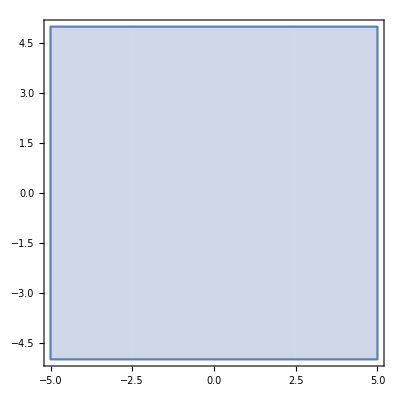

```mathematica
Clear[ℏ,m,σ]
ℏ=m=1;
σ=1;
k=1;
L =10σ;
tmax=10σ;
x0=0; y0=0;
Clear[ψ,V,Ω];
V[x_,y_]:=(x^2+y^2)/4
Ω=Rectangle[{-L/2,-L/2},{L/2,L/2}];
RegionPlot[Ω]
```

```mathematica
solution=NDSolveValue[{
 ⅈ ℏ D[ψ[t,x,y],t]==- ℏ^2/(2m)(D[ψ[t,x,y],{x,2}]+D[ψ[t,x,y],{y,2}]) + V[x,y]ψ[t,x,y],
(*Derivative[1,0,0][ψ][0,x,y]==0,*)
ψ[0,x,y]==ⅇ^(ⅈ k x)√(1/(2π σ^2)ⅇ^(-(x-x0)^2/(2 σ^2))ⅇ^(-(y-y0)^2/(2 σ^2))),
PeriodicBoundaryCondition[
ψ[t,x,y],x==-L/2,
TranslationTransform[{L,0}]
],
PeriodicBoundaryCondition[
ψ[t,x,y],y==-L/2,
TranslationTransform[{0,L}]
]
(*DirichletCondition[ψ[t,x,y]==0,True]*)
},ψ,{t,0,tmax},
(*{x,-L/2,L/2},
{y,-L/2,L/2}*)
{x,y}∈Ω
]
```

InterpolatingFunction[{{0., 10.}, {-5., 5.}, {-5., 5.}}, <>]

```mathematica
NIntegrate[Abs[solution[0,x,y]]^2,{x,y}∈Ω]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.00241

```mathematica
Plot3D[Abs[solution[2,x,y]]^2,{x,y}∈Ω,PlotRange->Full,PlotPoints->200]
```

-Graphics3D-

```mathematica
Monitor[plots=Table[Plot3D[Abs[solution[t,x,y]]^2,{x,y}∈Ω,PlotRange->{0,Abs[solution[0,0,0]]^2},PlotPoints->100],{t,0,tmax,tmax/20}];,N[t/tmax]]
```

```mathematica
ListAnimate[plots]
```

ToElementMesh::IncludePoints need to be a list of numeric coordinates not `1`: -- Message text not found -- (100)

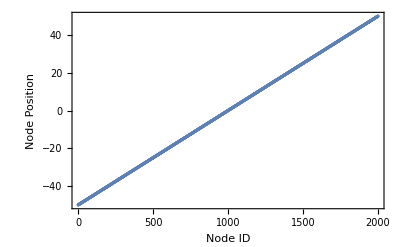

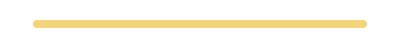

```mathematica
<<NDSolve`FEM`
L=100;
region=Line[{{-L/2},{L/2}}];
mesh=ToElementMesh[region,"IncludePoints"->100,"MaxCellMeasure"->0.1];
ListPlot[Union@Flatten@mesh["Coordinates"],Frame->True,FrameLabel->{{"Node Position",None},{"Node ID","Node Position vs Node ID"}}]
HighlightMesh[MeshRegion@mesh,0]
```

```mathematica
m=2;
tmax=L/2;
x0=0;σ=1;k=1;
solution=NDSolveValue[{
 ⅈ D[{ψ1[t,x],ψ2[t,x]},t] ==-ⅈ D[{ψ2[t,x],ψ1[t,x]},{x,1}]+{m ψ1[t,x],-m ψ2[t,x]}-0.01 D[{ψ1[t,x],ψ2[t,x]},{x,2}],
(*Derivative[1,0,0][ψ][0,x,y]==0,*)
{ψ1[0,x],ψ2[0,x]}==ⅇ^(ⅈ k x)√(1/(√(2π σ^2))ⅇ^(-(x-x0)^2/(2 σ^2))){1,-1}
(*DirichletCondition[ψ[t,x,y]==0,True]*)
},{ψ1,ψ2},{t,0,tmax},
(*{x,-L/2,L/2},
{y,-L/2,L/2}*)
{x}∈mesh
];
```

```mathematica
Manipulate[Plot[Evaluate[Total@(Abs[#[t,x]]^2&/@solution)],x∈mesh,PlotRange->Full],{{t,40},0,tmax}]
```